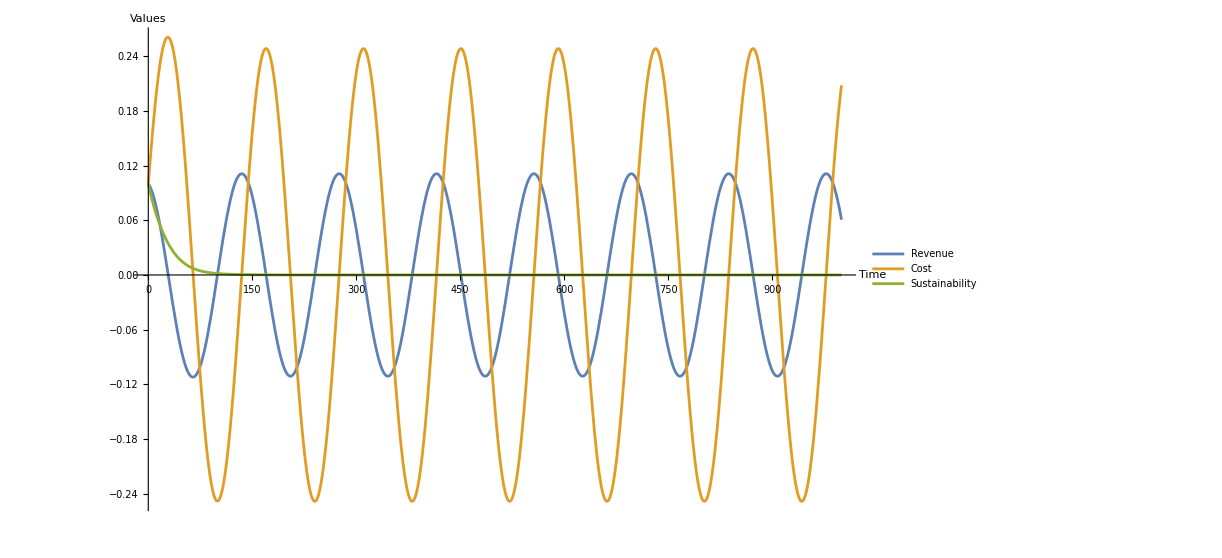

-Graphics3D-

```mathematica
Clear[r,c,s]

sol=NDSolve[
{
r'[t]==α s[t] -β c[t],
c'[t]==γ r[t]- δ s[t] c[t],
s'[t]==η s[t]r[t]-λ s[t],
r[0]==0.1,
c[0]==0.1,
s[0]==0.1,
λ==0.01,
η==0.04,
γ==0.02,
α==0.1,
δ==0.03,
β==0.05
},
{r,c,s},
{t,0,100000}
];

Plot[
Evaluate[{r[t],c[t],s[t]}/. sol],
{t,0,1000},
AxesLabel->{"Time","Values"},
PlotLegends->Placed[{"Revenue","Cost","Sustainability"},{Right,Top}]]

ParametricPlot3D[
Evaluate[{r[t],c[t],s[t]}/. sol],
{t,0,10000},
AxesLabel->{"r","c","s"},
BoxRatios->{1,1,1},
PlotLabel->"Phase Space Trajectory"]
```